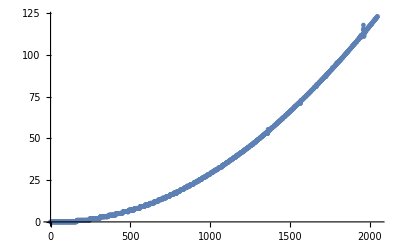

```mathematica
name := "bag"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
ListPlot[data]
```

```mathematica
nlm = NonlinearModelFit[data, a+b*x^2,{a,b},x]
```

FittedModel[-0.491508+0.0000295824 x^2]

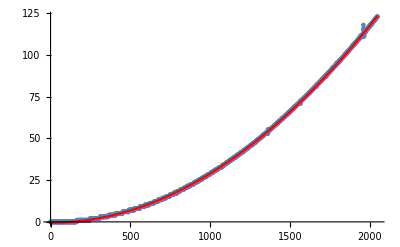

```mathematica
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
```